```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\shiyi\DiFfRG\Examples\QuarkMesonLPAprime\build\Tc

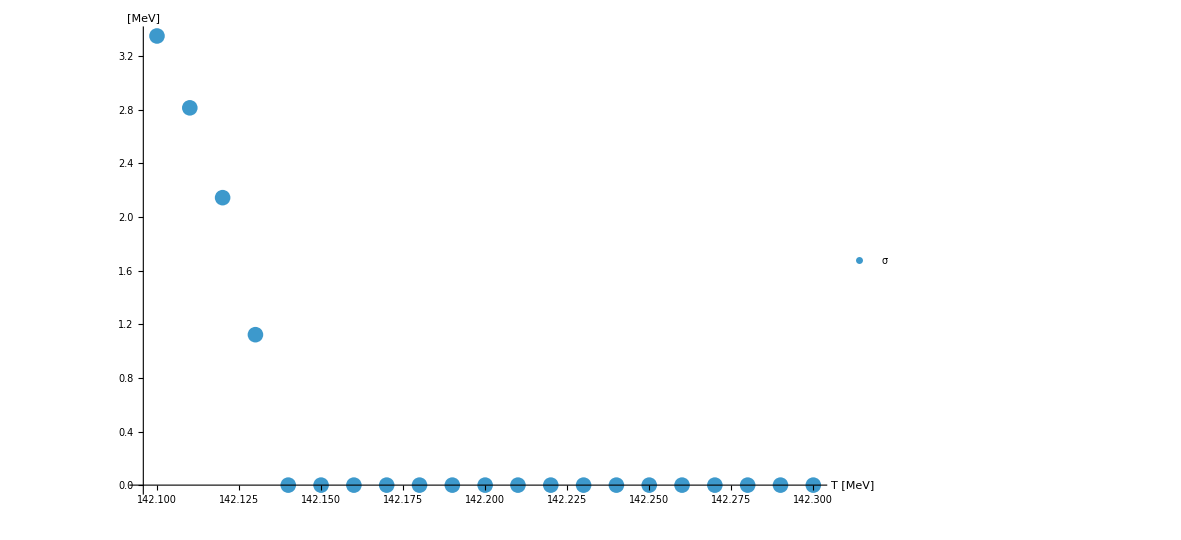

```mathematica
T=Table[i,{i,142.1,142.3,0.01}];
datasigmac=Table[Transpose[Import["./T"<>ToString[NumberForm[i*0.001,{Infinity,5}]]<>"_data_chiral.csv"]][[3]][[-1]]*1000,{i,142.1,142.3,0.01}];
ListPlot[{Transpose[{T,datasigmac}]},PlotLegends->{"σ","m_π","m_σ","m_q"},AxesLabel->{"T [MeV]","[MeV]"},PlotRange->All]
```

```mathematica
142.140MeV
```